```mathematica
$Assumptions = {x ∈ Reals, y ∈ Reals, v ∈ Reals, q ∈ Reals, θ ∈ Reals, j ∈ Reals, ψ ∈ Reals}
```

{q Cos[θ]∈ℝ,q Sin[θ]∈ℝ,True,q∈ℝ,θ∈ℝ,j∈ℝ,ψ∈ℝ}

```mathematica
b = FullSimplify[3/2 (Abs[α]^2 + v^2/2)(x^2+y^2) + 3 Abs[Δ]^2]
c = FullSimplify[1/4 x (x^2-3 y^2) (v^3- 3 v Abs[α]^2 + 2 Re[α^3]) - 3/2 (x^2+y^2) Re[Δ α^2 + 2 v α Conjugate[Δ]] + 2 Re[Δ^3]]
```

3/4 (x^2+y^2) (v^2+2 α Conjugate[α])+3 Δ Conjugate[Δ]

1/4 (x (x^2-3 y^2) (v^3+α^3-3 v α Conjugate[α]+Conjugate[α]^3)+8 Re[Δ^3]-6 (x^2+y^2) Re[α (α Δ+2 v Conjugate[Δ])])

```mathematica
α =FullSimplify[( -0.6938775510204075+0.4948716593053939I)]
Δ = 0.2857142857142856
```

-0.693878+0.494872 ⅈ

0.285714

```mathematica
Clear[Δ, j]
```

```mathematica
j=1
```

1

```mathematica
ϵ =FullSimplify[2 Sqrt[b/3]Cos[1/3 ArcCos[(3 c)/(2 b) Sqrt[3/b]] - j*2 π/3 ]]
```

√(q^2 (v^2+2 α Conjugate[α])+4 Δ Conjugate[Δ]) Cos[1/3 (2 j π-ArcCos[(1/(q^2 (v^2+2 α Conjugate[α])+4 Δ Conjugate[Δ]))^(3/2) (q^3 (v^3+α^3-3 v α Conjugate[α]+Conjugate[α]^3) Cos[3 θ]+8 Re[Δ^3]-6 q^2 Re[α (α Δ+2 v Conjugate[Δ])])])]

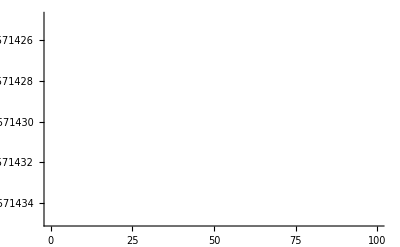

```mathematica
Plot[Re[ϵ], {q, 0, 100}]
```

```mathematica
ω = Exp[I 2 π/3]
x = q Cos[θ]
y = q Sin[θ]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
v = -2Re[α]
```

-2 Re[α]

```mathematica
FullSimplify[(v^3+α^3-3 v α Conjugate[α]+Conjugate[α]^3) ]
```

0

```mathematica
FullSimplify[ϵ]
```

Cos[1/3 (2 j π-ArcCos[(1/(q^2 (α^2+4 α Conjugate[α]+Conjugate[α]^2)+4 Δ Conjugate[Δ]))^(3/2) (-3 q^2 α^2 Δ+4 Δ^3-3 q^2 Conjugate[α]^2 Conjugate[Δ]+4 Conjugate[Δ]^3+12 q^2 (Δ Conjugate[α]+α Conjugate[Δ]) Re[α])])] √(4 Δ Conjugate[Δ]+2 q^2 (Im[α]^2+3 Re[α]^2))

```mathematica
Δ = Exp[I ψ]
```

ⅇ^(ⅈ ψ)

```mathematica
Clear[v]
```

```mathematica
FullSimplify[Series[ϵ, {q, 0, 2}]]
```

2 Cos[1/3 (2 j π-ArcCos[Cos[3 ψ]])]+1/2 (Cos[1/3 (2 j π-ArcCos[Cos[3 ψ]])] (Im[α]^2+3 Re[α]^2)+1/Abs[Sin[3 ψ]](Cos[3 ψ] (Im[α]^2+3 Re[α]^2)+Re[α Cos[ψ] (α-4 Re[α])]-Im[α (α+4 Re[α])] Sin[ψ]) Sin[1/3 (2 j π-ArcCos[Cos[3 ψ]])]) q^2+O[q]^3

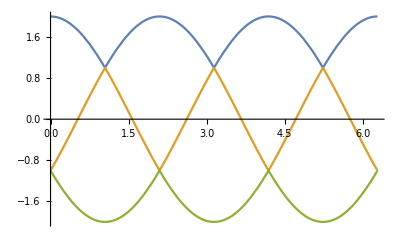

```mathematica
Plot[{2 Cos[1/3 (2 0 π-ArcCos[Cos[3 ψ]])], 2 Cos[1/3 (2 1 π-ArcCos[Cos[3 ψ]])], 2 Cos[1/3 (2 2 π-ArcCos[Cos[3 ψ]])]}, {ψ, 0, 2*Pi}]
```